```mathematica
SetDirectory[NotebookDirectory[]];
Import["init.wl"];
```

### Time-Dependent Dynamics

In this example, we examine how to propagate a time-dependent solution to the Schrodinger Equation and use the evolution to compute the spectrum of the potential from the wavefunction autocorrelation function. 
We begin by briefly reviewing time-dependent quantum mechanics, the solutions, ψ(x,t), to the time-dependent Schrodinger equation,

-ⅈ ℏ∂_t ψ[x,t]= -ℏ^2/(2m)∂_{x,2} ψ[x,t] + V[x]ψ[x,t]

This we can solve formally as,

ψ[x,t] = ∫⟨x|ⅇ^(-ⅈ H t/ℏ)|y⟩ψ[y,0]ⅆy

where H is the Hamiltonian operator, which we take to be time-independent. Since the kinetic energy operator and the potential operator do not commute, we cannot simply break the propagator (in brackets) into separate kinetic energy and potential energy contributions.

What we can do, however, is use the semi-group property of the propagator to write,

U(t_f,t_i)=U(δt_n)U(δt_(n-1))...U(δt_o) =𝒯 ∏_(i=1)^n U[δt_n]

where 𝒯 is the time-ordering operator and δ t_nis a short time interval δ t_n  = t_n-t_(n-1) and,

U(δ t)= ⟨x|ⅇ^(ⅈ H δ t /ℏ)|x'⟩

Since Ĥ =T̂ + V̂  we can use Baker-Campbell-Hausdorff relation to break the exponential into a product of three-exponentials.
This is the Trotter Product and is accurate to third order in δ t_i,

U(δ t_i)=ⅇ^(-ⅈ T t / 2)ⅇ^(-ⅈ V t)ⅇ^(-ⅈ T t / 2) + 𝔒[δ t^3]

To use this, we need to insert complete sets of states between each term,

U(δ t_i)=∫ ⟨x|ⅇ^(-ⅈ T t/2)|x'⟩⟨x'|ⅇ^(-ⅈ V t)|x'⟩⟨x'|ⅇ^(-ⅈ T t/2)|x''⟩ⅆx'

where we have taken advantage of the fact that V is simply a function of x.  Now, we insert complete sets of kinetic energy states Tn = ϵ_n n on either side of the kinetic energy terms,

U(δ t_i)=∑_(n=1)^N ∑_(m=1)^N ∫⟨x|n⟩ⅇ^(-ⅈ  ϵ_n t/2)⟨n|x'⟩ⅇ^(-ⅈ V(x')t)⟨x'|m⟩ⅇ^(-ⅈ ϵ_m t/2)⟨m|x''⟩ⅆx'

Lastly,  we approximate the integral over x' via Gaussian quadrature by using the DVR points and their associated weights,

U_kj(δ t_i)=∑_(n=1)^N T_nk ⅇ^(-ⅈ  ϵ_n δ t/2)∑_(i=i)^N T_ni ⅇ^(-ⅈ V_i δ t)∑_(m=1)^N T_mi ⅇ^(-ⅈ ϵ_m δ t/2)T_mj

Computationally, it is a bit more effective to break this into parts.

First, compute the contribution from the kinetic energy part.

F = ⅇ^(-ⅈ ϵ δt/2)

where F is a diagonal matrix.

Then, we hook everything together,

U_jk=(U^K.exp(-ⅈ δ t V).U^K)_jk

where, again, e^(-ⅈ V δ t), is a diagonal matrix computed by evaluating the potential over the DVR points, then exponentiating. 
After putting everything together we have an approximation for the quantum propagator over a short time-step.

```mathematica
tcheby[npts_Integer,xmin_,xmax_]:=Module[
{del,pts,t,fbrke,w},
del=xmax-xmin;
pts=N[Table[(i del)/(npts+1)+xmin,{i,npts}]];
t=N[Table[√(2./(npts+1)) Sin[((i j) π)/(npts+1)],{i,npts},{j,npts}]];
fbrke=N[Table[((i π)/del)^2,{i,npts}]];
w=N[Table[del/(npts+1),{i,npts}]];
Return[{pts,t,fbrke,w}]];
dv2fb[dvr_,t_]:=t.dvr.Transpose[t];
fb2dv[fbr_,t_]:=Transpose[t].fbr.t;
```

```mathematica
npts = 200;
xmin = -3.5;
xmax = 3.5;
xo= 1.5;
β= 0.5;
ℏ= 1;
δt= 0.02;
m= 1;

{pts,t,fbrke,w}=tcheby[npts,xmin,xmax];
fbrke = fbrke * ℏ^2/(2m);

v[x_]:=-5 x^2+x^4;
vdvr=Thread@v[pts];
hdvr =  (fb2dv[DiagonalMatrix[fbrke],t] + DiagonalMatrix[vdvr]);

expV =(Exp[-ⅈ v[pts] δt/ℏ])//Thread;
expK = (Exp[-ⅈ/ℏ fbrke δt/2])//Thread;
tTrans = Transpose[t];

uk = t.DiagonalMatrix[expK].tTrans;
u = uk.DiagonalMatrix[expV].uk;
```

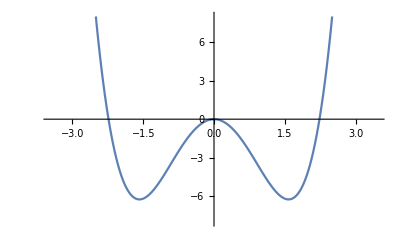

```mathematica
plotV=ListPlot[
Transpose[{pts,vdvr}],PlotRange->{-8,8},Joined->True,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["V",FontSize->20]},PlotLabel->MaTeX["\\text{Potential Energy Surface}",FontSize->20]
]
```

Now, we evolve the initial state,  ϕ_o, for  a few time-steps and compute the overlap of the time-evolve state with the initial state. 
What we’re interested in computing is the evolution of the overlap of the wavefunction at time t with the initial wavefunction.

c(t) =⟨ψ(0)|ψ(t)⟩ = ∑_(n=1)^N ⟨ψ(0)|n⟩  ⅇ^(ⅈ ω_n t)⟨ n|ψ(0)⟩

Thus, taking the Fourier transform of c(t)  produces a spectrum in ω where the peaks give the location of the energy eigenvalues and the intensities give the projection |⟨ψ(0)|n⟩|^2.

```mathematica
ψo[x_]:=(β/π)^(1/4) ⅇ^(-β (x-xo)^2);ϕo=Thread[ψo[pts]]; 
amp = 20.0;
norm=√(ϕo.ϕo);ϕo=ϕo/norm; ψt={ϕo}; ct={1};
ene = ϕo.hdvr.ϕo;
evolve={{ListPlot[Transpose[{pts,amp*ϕo+ene}],Joined->True,PlotRange->{{-4,4},{-8,8}},PlotStyle->Orange, DisplayFunction->Identity,Filling->ene,PlotLegends->{MaTeX["\\text{Re}\\phi(t)",FontSize->20]},
Epilog->Inset[MaTeX["t = "<>ToString[0.00],FontSize->20],{-1.0,6}],
AxesLabel->{MaTeX["x",FontSize->20],MaTeX["V",FontSize->20]},PlotLabel->MaTeX["\\text{Potential Energy Surface}",FontSize->20]],
ListPlot[Transpose[{pts,amp*Im[ϕo]+ene}],Joined->True,PlotRange->{{-4,4},{-8,8}},PlotStyle->Green,DisplayFunction->Identity,Filling->ene,PlotLegends->{MaTeX["\\text{Im}\\phi(t)",FontSize->20]}]}};
nsteps=20;
 ϕt=ϕo;
 Do[ϕt=u.ϕt;c=ϕo.ϕt;ct=Append[ct,c];If[Mod[n,1]==0, ψt=Append[ψt,ϕt];rePlot=ListPlot[Transpose[{pts,amp*Re[ϕt]+ene}],Joined->True,PlotRange->{{-4,4},{-8,8}},PlotStyle->Orange, DisplayFunction->Identity,Filling->ene,PlotLegends->{MaTeX["\\text{Re}\\phi(t)",FontSize->20]},
Epilog->Inset[MaTeX["t = "<>ToString[n δt],FontSize->20],{-1.0,6}],
AxesLabel->{MaTeX["x",FontSize->20],MaTeX["V",FontSize->20]},PlotLabel->MaTeX["\\text{Potential Energy Surface}",FontSize->20]];
imPlot=ListPlot[Transpose[{pts,amp*Im[ϕt]+ene}],Joined->True,PlotRange->{{-4,4},{-8,8}},PlotStyle->Green,DisplayFunction->Identity,Filling->ene,PlotLegends->{MaTeX["\\text{Im}\\phi(t)",FontSize->20]}];evolve=Append[evolve,{rePlot,imPlot}]],{n,nsteps}]; ct1=ct;
```

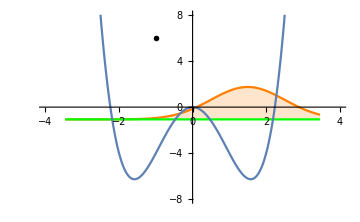
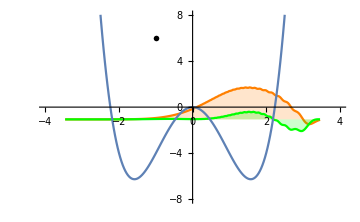
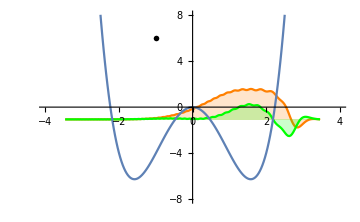
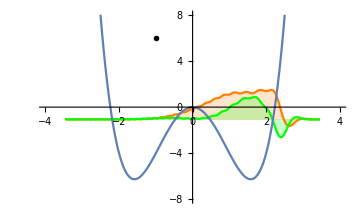
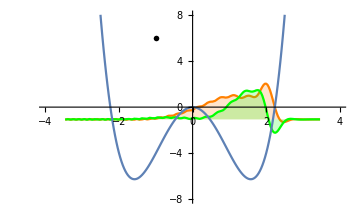
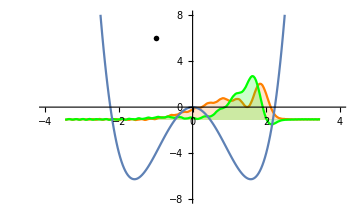
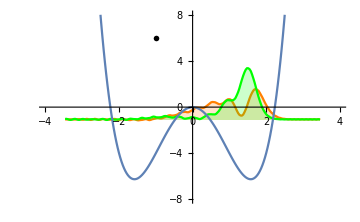
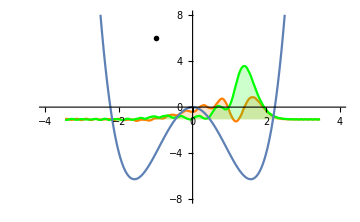

```mathematica
TableForm@Table[e=evolve[[i]]; Show[e[[1]],e[[2]],plotV,PlotRange->{{-4,4},{-8,8}},ImageSize->Medium],{i,1,20,2}]
```